# Min-Heap Implementation

In this notebook, I’ll store the core functions for a min-heap implementation. All modifications are in-place, and for convenience in this notebook, the Heap is the global variable heap.

All functions except for extractmin are quite straightforward, and function optimally if implemented without constructs (Block, Module, etc.).  Implementation and algorithmic details can be found in each section.

## HeapQ

Tests if a is a min-Heap in O(n) time complexity. Checks parent node for min-heap property at all nodes.

```mathematica
HeapQ[a_List]:=
And@@Table[a⟦Floor[i/2]⟧≤ a⟦i⟧, {i, 2, a//Length}]
```

## heapifyDown

Swaps elements downwards until node satisfies Min-Heap property.

```mathematica
heapifyDown[i_]:=With[ {n = heap//Length},
Which[ 
	n< 2i,
		heap,
	(*at leaf*)
	
	n≤2i && heap⟦i⟧≥ heap⟦2i⟧, 
		{heap⟦i⟧, heap⟦2i⟧}={heap⟦2i⟧, heap⟦i⟧};
		heapifyDown[2i];,
	(*only left child*)
	
	n≤2i && heap⟦i⟧≤  heap⟦2i⟧, 
		heap,
	(*only left child, satisfied*)
	
	heap⟦i⟧≤ heap⟦2i⟧ && heap⟦i⟧≤ heap⟦2i+1⟧, 
		heap,
	(*property satisfied*)
	
	heap⟦i⟧≥Min[heap⟦2i⟧, heap⟦2i+1⟧] && heap⟦2i⟧≤  heap⟦2i+1⟧,
		{heap⟦i⟧, heap⟦2i⟧}={heap⟦2i⟧, heap⟦i⟧};
		heapifyDown[2i];,
	(*swap with left child*)
	
	heap⟦i⟧≥  Min[heap⟦2i⟧, heap⟦2i+1⟧] && heap⟦2i⟧>heap⟦2i+1⟧,
		{heap⟦i⟧, heap⟦2i+1⟧}={heap⟦2i+1⟧, heap⟦i⟧};
		heapifyDown[2i+1];
	(*swap with right child*)
 ]
]
```

## heapifyUp

Swaps elements upwards until property is satisfied, starting at position i.

```mathematica
heapifyUp[i_]:=Which[

i==1,
	heap,
(*at root*)

heap⟦i⟧≥ heap⟦Floor[i/2]⟧,
	heap,
(*satisfies minHeap prop, return*)

heap⟦i⟧≤ heap⟦Floor[i/2]⟧,
	{heap⟦i⟧, heap⟦Floor[i/2]⟧}={heap⟦Floor[i/2]⟧, heap⟦i⟧};
	heapifyUp[Floor[i/2]];
(*swap with parent, if greater*)
]
```

## hInsert

```mathematica
hInsert[element_]:=(
AppendTo[heap, element];
heapifyUp[heap//Length];
)
```

## buildH

```mathematica
buildH[n_]:=Map[heapifyDown[#]&, Range[Floor[(heap//Length)/2], 1, -1]]
```

## extractMin

ExtractMin was implemented with an amortized algorithm to compensate for the linear time pop operation. The algorithm relies on a global deletion counter dcount, and works as follows:

### Algorithmic Details

#### Algorithm

Increment dcount;

Store the first element, then Swap it with the last element;

Set the new last element to infinity;

If dcount more than half the length of the heap,

Reset dcount to 0, Select out all infinity elements in O(N);

Rebuild the heap applying buildH;

HeapifyDown the first element.

Every time extractMin is performed, the counter is incremented and a null element ∞ is left at the bottom (maintaining heap size) . After n such operations, the asymptotic cost of a Select operation is O(n), making the amortized cost constant.

### Definition

```mathematica
extractMin := With[{n=heap//Length},

dcount++;

x = heap⟦1⟧;

(*swap last element*)
{heap⟦1⟧, heap⟦n⟧}={heap⟦n⟧, heap⟦1⟧};

(*set infinity at the end*)
heap⟦n⟧ = Infinity;

(*divide into amortization cases*)
If[dcount > n / 2, 
	dcount = 0; 
	heap = Select[heap, #≠ Infinity&];
	buildH[heap];
];

heapifyDown[1];

x
]
```

## Tests

### heapifyDown

```mathematica
l={0.0007031965668341239,0.0005921175468384416,0.0005036481763494314,0.00037944097276922985,0.000296915752069877,0.00016909829800393263,0.0001264681685308687,0.00009638274781634547}
```

{0.000703197,0.000592118,0.000503648,0.000379441,0.000296916,0.000169098,0.000126468,0.0000963827}

```mathematica
data=Riffle[Range[2, 8], Reverse[l]]//Partition[#, 2]&
```

{{2,0.0000963827},{3,0.000126468},{4,0.000169098},{5,0.000296916},{6,0.000379441},{7,0.000503648}}

```mathematica
fit=Fit[data, {1, x}, x]
```

-0.00011383+0.0000835161 x

```mathematica
p2=Plot[fit, {x, 2, 7}, PlotStyle->Orange];
```

```mathematica
p1=ListPlot[data, PlotLabel->"LogLinear Plot of HeapifyDown Evaluation Time", AxesLabel->{"10^i elements", "time[s]"}];
```

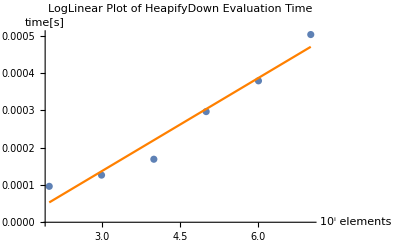

```mathematica
Show[p1, p2]
```